```mathematica
data=Import["C:\\Users\\pcmultimedia\\Documents\\3_ano_2_semestre\\LFEA\\Vida_media_muao\\range.txt",{"Data",{All},{1,2}}];
```

```mathematica
f=Interpolation[data]
```

InterpolatingFunction[{{111.125, 1000.}}, <>]

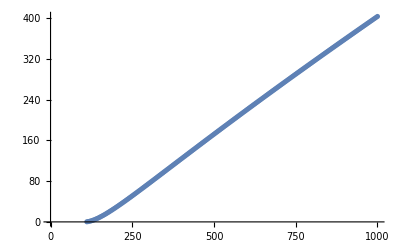

```mathematica
ListPlot[f]
```

```mathematica
f[477.64718792397485]
```

161.262

### Energia tipica de um muao que para ao passar em B e S1 - Muoes com energia menor que passem em B e S1 sao parados

```mathematica
FindRoot[f[x]==10.9567,{x,112}]
```

{x→155.914}

```mathematica
Emax2=155.914
```

155.914

### Energia tipica de um muao que para ao passar apenas em B

```mathematica
FindRoot[f[x]==6.71399,{x,112}]
```

{x→142.781}

```mathematica
Emax1=142.781
```

142.781

### Energia tipica de um muao que para ao passar apenas em S1

```mathematica
FindRoot[f[x]==1.9116,{x,112}]
```

```mathematica
{x->123.4479584396877}
```

{x→123.448}

```mathematica
Emin2=123.448
```

123.448

```mathematica
Emin1=105.658
```

105.658

## Rácios

### Situação 1 (B apenas) --> 0.759314 Situação 2 (B e S1) --> 0.240686

```mathematica
r1=0.759314
r2=0.240686
```

0.759314

0.240686

## Intervalos de energia médios

#### Limite superior:

```mathematica
Emaxmed=Emax1*r1+Emax2*r2
```

145.942

#### Limite inferior

```mathematica
Eminmed=Emin1*r1+Emin2*r2
```

109.94